Mathematical Techniques in Evolution and Ecology

# Functions and approximations

Based on Primer 1 in Otto and Day (2007)

Spring Quarter 2015
Simon Aeschbacher
saeschbacher@ucdavis.edu

## Outline

### Goal

To revisit some common functional forms

To learn some guidelines for simplifying and approximating models

### Concepts

Linear, quadratic, and polynomial functions

Rational, bell-shaped, and sigmoidal (S-shaped) functions

Sequences and series

Linear approximations (1st order Taylor series)

More general approximations (higher-order Taylor series)

## Motivation

In practice, we will often want (or have to) make approximations or simplifying assumptions when constructing and analysing mathematical models. The reasons for this are twofold:

We want to abstract only the parts that are important w.r.t. our question(s)

Example: The appropriate scale of a map for a road trip is different from the scale of a map for a hike. So is the amount of detail and type of information you expect on the map.

Simplification is often necessary for mathematical analysis. This is linked to a limited amount of time you have to analalyse a model, and to the difficulty of making sense of very complicated and long formulae.

Example: To measure the length of a route from A to B on your map, it may be ok to measure the straight line from A to B, as long as the route does not curve too much and there is not too much of a difference in altitude.

Approximation and simplification imply compromises. Our goal is to learn how to make these choices in an appropriate way. Throughout the modelling process and when interpreting the results, it is important to be aware of these choices.

## Functions and their forms

### Frame of reference

Model processes explicitly within a frame of reference (i.e. a certain level of biological complexity or phenomena)

Link to processes/phenomena at other levels implicitly using functions that behave in a way that is consistent with our understanding of these phenomena

Example: In our squirrels example, the frame of reference was the (female) squirrel population on campus, where we modelled birth, death, and immigration. We did not explicitly model the cyclists nor the squirrel population in the Arboretum, which we assumed was the source of immigrants.

The phenomenological modelling approach: a function is used to describe underlying/external biological processes

Fewer parameters

Often easier to understand

Intuition about underlying/external process needed

The mechanistic modelling approach: the details at another level are explicitly tracked

More parameters

More detailed, potentially more difficult to understand

Need more data to estimate the parameters

### The logistic model as an example of the phenomenological approach

We did not explicitly model the behaviour of individuals during the consumption of resources explicitly, nor the resource

Instead, we modelled competition implicitly by assuming that the number of surviving offspring per parent, R(n), decreases in a certain form as the population size n increases. We chose this to be a linear decrease, i.e. R(n)=1+r_d-r_d/K n(t), but alternative choices are possible:

```mathematica
funcRPlot (* solid blue: linear, long-dashed orange: quadratic, short-dased green: exponential,thick red: sigmoidal *)
```

### Some popular functions

A good guiding principle when modelling a process implicitly is to choose a function that is as simple as possible, but still has the desired shape. The following functions are commonly used in biology; they represent a variety of different shapes.

#### Linear function

f(x)=bx+c

Describes a straight line with slope b and intercept c

```mathematica
linFuncPlot
```

#### Quadratic function

f(x)=a x^2+b x+c

Describes a parabola that curves up (a>0; convex, solid blue) or down (a<0; concave, dashed orange)

Where is the maximum (if a<0) / minimum (if a>0) located?

```mathematica
quadFuncPlot
```

#### Polynomial function

Linear and quadratic functions are special cases of the polynomial functions. The nth-degree polynomial is a function of the form

f(x)=∑_(i=0)^n a_i x^i.

Polynomials typically have n-1 extrema (i.e. minima or maxima)

The behaviour as x goes to positive or negative infinity is determined by the sign of the term with the highest power, a_n x^n.

#### Exponential function

f(x)=c ⅇ^(a x)

Describes an exponential rise or fall

If a>0, the function increases exponentially (solid blue)

If a<0, the function decreases exponentially (dashed orange)

At what value does it cross the y axis (i.e. what is the intercept)?

```mathematica
expFuncPlot
```

#### Rational function

If the desired function is nearly linear for small x, but reaches a constant value (an asymptote) as x becomes large, one choice is a rational function:

f(x)=(a x+c)/(b x+d).

What is the intercept (i.e. the value when x=0)

What is the slope of the increase/decrease when x is very small?

What value does f(x) converge to as x becomes very large?

In general, a rational function is any polynomial divided by a polynomial

```mathematica
ratFuncPlot
```

#### Bell-shaped function

A possible choice for a bell-shaped function is

f(x)=m ⅇ^(-(x-b)^2/a).

At what value of x does it have an extremum? What is f(x) at this value of x?

Larger values of a cause the bell to be wider (dashed orange), smaller values of a make it more narrow (solid blue)

Note the relation to the normal distribution, where a=2 σ^2(twice the variance), b=μ (the mean), and m=1/√(2π σ^2).

In general, a rational function is any polynomial divided by a polynomial

```mathematica
bellFuncPlot
```

#### S-shaped (sigmoidal) function

A popular choice for a sigmoidal function is the so-called logistic function,

f(x)=(c ⅇ^(a x))/(c ⅇ^(a x)+(1-c)).

Here, c is a fraction (0<c<1) telling us how far the way up the “S” the function is at x=0

If a>0, the function rises to 1 as x increases from 0 (solid blue)

If a<0, the function falls to 0 as x increases from 0 (reverse S-shape; dashed orange)

The magnitude of a determines the sharpness of the rise/fall

```mathematica
sigmFuncPlot
```

### Rule P1.1: Changing the shape of a function

The following rules can be used to alter a function f(x) to match a desired shape. This can be very useful in practice!

To shift a function to the right or left by an amount of d, replace x by (x-d) or (x+d), respectively

To increase or decrease the height of a function by an amount of d, replace f(x) by f(x)+d or f(x)-d, respectively

To scale a function along the horizontal (x) axis by a factor d, replace x by x/d. Stretching occurs if d>1, shrinking occurs if d<1.

To scale a function along the vertical (y) axis by a factor of d, replace f(x) by d f(x). Stretching occurs if d>1, shrinking occurs if d<1.

To reflect a function across the horizontal (x) axis, replace f(x) by -f(x)

#### Example

Imagine modelling the effect of an inhibitor on the level of phosphorus within a cell. Assume that the level of phosphorus P(x) declines exponentially at rate α from an initial level P_max, as the concentration x of the inhibitor increases. Assume further that P(x) asymptotes at some minimum level P_min as x becomes very large. How can you modify the exponential function introduced above to model this? In other words, what are the parameters c and a in this example?

## Linear approximations

When analysing models, we often ask: Is it possible to choose a simpler function that approximates a complicated function, at least within a region of interest? Here, the “region of interest” may refer to

a variable lying near a particular point (e.g. the population size is near 0 or near carrying capacity)

a parameter being near a particular value (e.g. the selection coefficient is near 0)

Knowing how to approximate an equation accurately is a very important technique in modelling!

The most straightforward (and often sufficient!) approximation is based on the idea that any curve looks roughly like a line if we zoom in close enough. Hence, given a complicated function f(x), we want to approximate it by a function f̃(x) of the form

f̃(x)=b x+c

such that the approximation is “good” when x is close to a, and such that the match is perfect if x=a, i.e.

f̃(a)=f(a).

### Examples

Let us work out two examples:

Derive the linear approximation to the example of a phosphorous inhibitor above, assuming that the concentration x of the inhibitor is low.

Derive a linear approximation to the discrete-time recursion equation of the haploid selection model, Δp=s_d p(t)(1-p(t))/(1+s_d p(t)), assuming that selection is weak.

### Recipe P1.1: Approximating a function f(x) by a line at x=a

For points x near a, the function f(x) can be approximated by the line

f̃(x)=f(a)+(ⅆf/ⅆx|_(x=a))(x-a).

This is also called a linear Taylor series approximation (see next subsection).

## The Taylor series

Linear approximations (previous section) are a special case of a much more general, very powerful technique, the Taylor series approximation. The Taylor series

allows us to understand when a function can be appproximated

provides a method to obtain approximations to any order of accuracy

is used very often in biological modeling

We start with two definitions.

### Definition P1.8: Sequence

A sequence is a list of mathematical terms, typically labelled by some index, e.g. a_0,a_1,a_2,...,a_k.
Examples:

(i) Sequence of squared natural numbers: 0,1,4,9,...,k^2

(ii) Geometric progression: 1/2^0, 1/2^1,1/2^2,1/2^3,...,1/2^k

### Definition P1.9: Series

A series is a sum of the terms of a sequence (e.g. a_0+a_1+a_2+...+a_k).
Examples:

(i) Series of squared natural numbers: 0+1+4+9+...+k^2=∑_(a=0)^k a^2

(ii) Geometric series: 1/2^0+1/2^1+1/2^2+1/2^3+...+1/2^k=∑_(i=o)^k (1/2)^i

If there are an infinite number of terms, we say it is an infinite series, and represent it as

a_0+a_1+a_2+...

or

∑_(i=0)^∞ a_i (more precisely: lim_(n→∞) ∑_(i=0)^n a_i).

### Convergence and divergence

If this sum approaches a particular value (other than positive or negative infinity), the infinite series is said to converge. If the sum keeps growing or shrinking for ever, the infinite series is said to diverge.

Decide if the following infinite series are convergent or divergent. If a series is convergent, find out which value it converges to.

The sum of all integers, 1+2+3+...

The sum of squared natural numbers, 0+1+4+9+...=∑_(a=0)^∞ a^2

The infinite geometric series, ∑_(i=0)^∞ a^i, if a=1/2

### Expressing a function as a power series

Most functions can be rewritten as the infinite series

f(x)=b_0+b_1 x+b_2 x^2+...

This infinite series is referred to as a power series, because it contains terms that are integer powers of x.

Suppose we want to focus on the behaviour of f(x) around a particular point a. This corresponds to shifting the power series along the x axis by an amount a. From Rule P1.1, we therefore have

f(x)=b_0+b_1(x-a)+(b_2(x-a))^2+...

This is referred to as “a power series in x, around the point x=a”.

All that is left to do is to find the coefficients b_i. The Taylor series does just that...

### Definition P1.10 The Taylor series of a function f(x)

Most functions f(x) can be represented as a power series around the point x=a given by

f(x)=b_0+b_1(x-a)+(b_2(x-a))^2+...,

whose coefficients are given by

b_i=1/(i!)(ⅆ^i f)/(ⅆ x^i)|_(x=a),

where ⅆ^i f/ⅆ x^i is the ith derivative of f(x) w.r.t. x. The coefficients b_i are evaluated at x=a and do not depend on x. This is called the Taylor series of the function.

For this to work, all derivatives ⅆ^i f/ⅆ x^i must be finite. This restriction determines which functions can and cannot be represented by a Taylor series.

Remark: Because 0! =1 (by definition) and the 0th derivative of a function is the function itself, the first three terms in a Taylor series are

b_0=1/(0!)(ⅆ^0 f)/(ⅆ x^0)|_(x=a)=f(a)

b_1=1/(1!)(ⅆ^1 f)/(ⅆ x^1)|_(x=a)=ⅆf/ⅆx|_(x=a)

b_2=1/(2!)(ⅆ^2 f)/(ⅆ x^2)|_(x=a)=1/2(ⅆ^2 f)/(ⅆ x^2)|_(x=a)

#### Example 1: f(x)=ⅇ^x

Derive the Taylor series of the exponential function f(x)=ⅇ^x around the point x=a=0.

Does the series converge?

Repeat this for the more general version f(x)=c ⅇ^(a x).

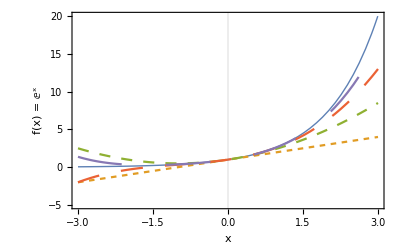

```mathematica
plotSeriesExp (* Thick blue: f(x); dashed curves: linear, quadratic, cubic, and quartic approximation with increasing amount of dashing. *)
```

#### Example 2: f(x)=ln(x)

Derive the Taylor series of the logarithmic function f(x)=ln(x) around the point x=a=1.

Does the series converge?

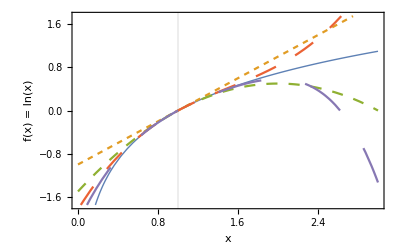

```mathematica
plotSeriesLog (* Thick blue: f(x); dashed curves: linear, quadratic, cubic, and quartic approximation with increasing amount of dashing. *)
```

### Recipe P1.2 Obtaining the Taylor series approximation of a function f(x)

Most functions f(x) can be approximated around the point x=a by  truncating the Taylor series to the degree of accuray desired and ignoring remaining terms. If the terms that are ignored are on the order of (x-a)^i, we write these terms as (O(x-a))^i. Doing so clarifies the degree of accuracy of the approximation.

The crudest approximation is the constant approximation:

f(x)=f(a)+O(x-a).

It is correct only at x=a and provides no information about what happens as we move x even just a little away from a.

A more accuracte approximation is the line, i.e. a linear approximation:

f(x)=f(a)+(ⅆf/ⅆx|_(x=a))(x-a)+(O(x-a))^2.

The term ⅆf/ⅆx|_(x=a) is the slope and determines whether the function increases or decreases as we move x away from a.

Including the next order gives a quadratic approximation:

f(x)=f(a)+(ⅆf/ⅆx|_(x=a))(x-a)+1/2((ⅆ^2 f)/(ⅆ x^2)|_(x=a))(x-a)^2+(O(x-a))^3.

The approximation implies that the function curves upward around x=a when ⅆ^2 f/ⅆ x^2|_(x=a) is positive (convex), but downward if it is negative (concave).

In practice, we often ignore the O() terms, but replace the “equals” sign by an “approximately equals” sign, i.e.

f(x)=f(a)+(ⅆf/ⅆx|_(x=a))(x-a)+(O(x-a))^2

can be written as

f(x)≈f(a)+(ⅆf/ⅆx|_(x=a))(x-a),

which is shorter, but it may not be immediately clear of what order the approximation is.

## Some remarks on the Taylor series approximation

If a Taylor series does not converge in the region of interest, it is of little help. Even if a Taylor series does not converge for all values of x, it may still do so for the interval of interest. To get a feeling of whether a series will converge, consider the terms ⅆ^i f/ⅆ x^i|_(x=a)(x-a)^i/i!. As i increases, the subterms (x-a)^i/i! eventually go to zero, because the factorial function in the denominator rises faster than the power in the numerator. Consequetially, as long as the derivative terms  ⅆ^i f/ⅆ x^i|_(x=a) do not increase too dramatically as i increases, the series will converge at least for values of x near a.

In practice, we can therefore “almost always” approximate a function f(x) near the point x=a using the first few terms of the Taylor series.

In most cases, the more terms are included in Taylor series approximation, the more accurate the approximation tends to be. We must be careful if the series does not converge over the full range of x, though.

We only expect a Taylor series approximation to be accurate near the point a around which it is taken. If convergence is an issue, the Taylor series can give a completely wrong answer for x that are not close to a. Technically, the radius of convergence defines the boundary.

The Taylor series can fail completely for functions if their derivatives do not exist at certain points and/or if higher-order derivatives are too large to ignore. Such functions tend to be jagged, with discontinuities (“kinks”), or have points where the function goes off to plus or minus infinity (“poles”).

It is a good idea to plot the original function and along with its approximation to spot potential issues.

## Problem assignment

Determine the functions R(n) for the reproductive factor in the logistic growth model, such that the shape of the functions is consistent with the first figure above. In each case, choose the parameters such that the intercept is R(0)=1+r, and the value when N=K is R(K)=1. Specifically, derive

(a) A function that declines exponentially to zero.

(b) A quadratic function with a maximum at n=0.

(c) A reverse-S-shaped function that declines from 1+r to zero. Keep a arbitrary, and use Rule P1.1 above to increase the intercept to 1+r.

Use Recipe P1.1 to confirm the following linear approximations:

(a) ⅇ^r≈1+r		assuming r is small

(b) 1/(1+s)≈1-s		assuming s is small

(c) ln(t)≈t-1		assuming t is near 1

(d) 1/x≈1/a-1/a^2(x-a)	assuming x is near a

## Initialisation cells

```mathematica
linRFunc[n_,rd_,KK_]:=1+rd-rd/KK n
quadRFunc[n_,rd_,KK_]:=1+rd-rd/KK^2 n^2
expRFunc[n_,rd_,KK_]:=(1+rd)(1+rd)^(-n/KK)

refSRFunc[n_,rd_,KK_,a_]:=(1+rd)ⅇ^(a n)/((1-(rd ⅇ^(a KK))/(1-ⅇ^(a KK)))ⅇ^(a n)+(rd ⅇ^(a KK))/(1-ⅇ^(a KK)))
```

```mathematica
(1+rd)ⅇ^(a n)/(c ⅇ^(a n)+1-c)/.{n->KK}
```

(ⅇ^(a KK) (1+rd))/(1-c+c ⅇ^(a KK))

```mathematica
FullSimplify[Solve[(ⅇ^(a KK) (1+rd))/(1-c+c ⅇ^(a KK))==1,c]]
```

{{c→1+rd+rd/(-1+ⅇ^(a KK))}}

This can be written as c=1-(r_d ⅇ^(a K))/(1-ⅇ^(a K)). Inserting into (ⅇ^(a K)(1+r_d))/(1-c+c ⅇ^(a K)) yields

(1+r_d)ⅇ^(a n)/((1-(r_d ⅇ^(a K))/(1-ⅇ^(a K))) ⅇ^(a n)+(r_d ⅇ^(a K))/(1-ⅇ^(a K))).

```mathematica
funcRPlot:=Manipulate[
Plot[
{linRFunc[n,rd,100],quadRFunc[n,rd,100],expRFunc[n,rd,100],refSRFunc[n,rd,100,a]},{n,0,2.5 100},
PlotRange->{{0,2.5 100},{0,1+rd+0.01}},
GridLines->{{100},{1}},
Frame->True,
FrameLabel->{{"Reproductive factor, R(n)",""},{"Population size, n(t)","K = 100"}},
LabelStyle->Directive[FontSize->14,FontFamily->"Helvetica"],
PlotStyle->{{},Dashing[0.05],Dashing[0.02],Thickness[Large]}
],
{{rd,0.75},0.,2.5}(*,{{KK,100},0,1000}*),{{a,-.1},-1,0}
]
```

```mathematica
linFunc[x_,b_,c_]:=b x+c
quadFunc[x_,a_,b_,c_]:=a x^2+b x+c
expFunc[x_,a_,c_]:=c ⅇ^(a x)
ratFunc[x_,a_,b_,c_,d_]:=(a x+c)/(b x+d)
bellFunc[x_,a_,b_,max_]:=max ⅇ^(-(x-b)^2/a)
sigmFunc[x_,a_,c_]:=(c ⅇ^(a x))/(c ⅇ^(a x)+(1-c))
```

```mathematica
sigmFuncPlot:=Manipulate[
Plot[{sigmFunc[x,a1,c1],sigmFunc[x,a2,c2]},{x,0,15},
PlotRange->{{0,10},{0,1}},
Frame->True,
FrameLabel->{{"f(x)",""},{"x","S-shaped (sigmoidal) function"}},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14],
PlotStyle->{{},Dashed}
],
{{a1,1},0.,10.},{{a2,-1},-10.,0.},{{c1,0.01},0.001,0.999},{{c2,0.99},0.001,0.999}
]
```

```mathematica
bellFuncPlot:=Manipulate[
Plot[{bellFunc[x,a1,b,max],bellFunc[x,a2,b,max]},{x,-10,10},
PlotRange->{{-1.5,1.5},{-2.5,2.5}},
Frame->True,
FrameLabel->{{"f(x)",""},{"x","Bell-shaped function"}},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14],
PlotStyle->{{},Dashed}
],
{{a1,0.25},0.001,2},{{a2,0.5},0.001,2},{{b,0},-1,1},{{max,2.25},-5,5}
]
```

```mathematica
ratFuncPlot:=Manipulate[
Plot[{ratFunc[x,a1,1,c,1],ratFunc[x,a2,1,c,1]},{x,0,10},
PlotRange->{{0,2},{-5,5}},
Frame->True,
FrameLabel->{{"f(x)",""},{"x","Rational function"}},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14],
PlotStyle->{{},Dashed}
],
{{a1,4},-10,10},{{a2,-4},-10,10},(*{{b,1},-10,10},*){{c,1},-10,10}(*,{{d,1},-10,10}*)
]
```

```mathematica
expFuncPlot:=Manipulate[
Plot[{expFunc[x,a1,c],expFunc[x,a2,c]},{x,-10,10},
PlotRange->{{-2.5,2.5},{0,5}},
Frame->True,
FrameLabel->{{"f(x)",""},{"x","Exponential function"}},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14],
PlotStyle->{{},Dashed}
],
{{c,1},0,4},{{a1,1},0,10},{{a2,-1},-10,0}(*,{{b,0},0,10}*)
]
```

```mathematica
quadFuncPlot:=Manipulate[
Plot[{quadFunc[x,a1,b,c],quadFunc[x,a2,b,c]},{x,-10,10},
PlotRange->{{-5,5},{-10,10}},
Frame->True,
FrameLabel->{{"f(x)",""},{"x","Quadratic function"}},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14],
PlotStyle->{{},Dashed}
],
{{c,1},-10,10},{{a1,1},0,10},{{a2,-1},-10,0},{{b,0},0,10}
]
```

```mathematica
linFuncPlot:=Manipulate[
Plot[{linFunc[x,b1,c],linFunc[x,b2,c]},{x,0,10},
PlotRange->{Full,{-10,10}},
Frame->True,
FrameLabel->{{"f(x)",""},{"x","Linear function"}},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14],
PlotStyle->{{},Dashed}
],
{{c,1},0,10},{{b1,1},0,10},{{b2,-1},-10,0}
]
```

```mathematica
plotSeriesExp:=Plot[
{Exp[x],1+x,1+x+1/2 x^2,1+x+1/2 x^2+1/6 x^3,1+x+1/2 x^2+1/6 x^3+1/24 x^4},{x,-3,3},
PlotRange->{{-3,3},{-5,20}},
GridLines->{{0},{}},
PlotStyle->{{Thickness[Large]},{Dashing[0.01]},{Dashing[0.02]},{Dashing[0.04]},{Dashing[0.08]}},
Frame->True,
FrameLabel->{"x","f(x) = ⅇ^x"},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14]
]
```

```mathematica
plotSeriesLog:=Plot[
{Log[x],(x-1),(x-1)+(-1/2(x-1)^2),(x-1)+(-1/2(x-1)^2)+(1/3(x-1)^3),(x-1)+(-1/2(x-1)^2)+(1/3(x-1)^3)+(-1/4(x-1)^4)},{x,0,3},
PlotRange->{Full,{-1.75,1.75}},
GridLines->{{1},{}},
PlotStyle->{{Thickness[Large]},{Dashing[0.01]},{Dashing[0.02]},{Dashing[0.04]},{Dashing[0.08]}},
Frame->True,
FrameLabel->{"x","f(x) = ln(x)"},
LabelStyle->Directive[FontFamily->"Helvetica", FontSize->14]
]
```